```mathematica
k=6000
```

6000

```mathematica
sCurve[t_,sigmaS_,ht_,taut_,tauf_]:=tauf*(1+sigmaS Exp[-ht/t]taut)/(1+sigmaS Exp[-ht/t]tauf)
```

```mathematica
Manipulate[
Plot[sCurve[t,sigmaS,ht,taut,tauf],{t,270,400}],
{sigmaS,4*^9,5*^9},
{ht,4000,10000},
{taut,0.1,0.8},
{tauf,0.1,0.8}
]
```

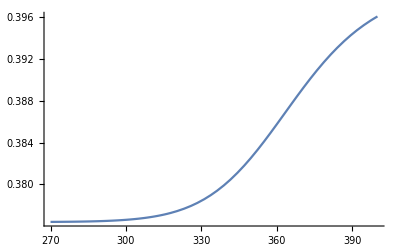

```mathematica
Plot[sCurve[t,4.1*^9,7752,0.3994,0.3764],{t,270,400}]
```